W[T,X]=-A ⅇ^(-a T)+w0-B ⅇ^(-b T) X

K[T,X]=X Conjugate[X]-3 Log[T+Conjugate[T]]

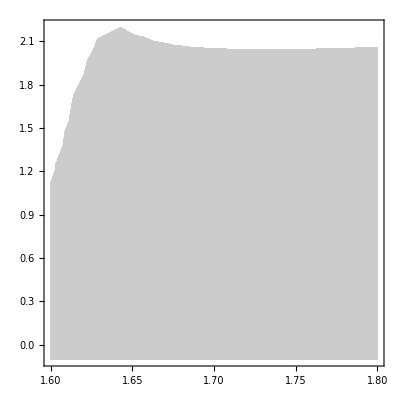

-Graphics3D-

x=1.05

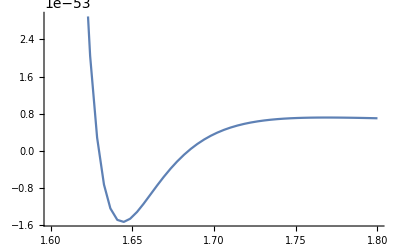

```mathematica
Clear[zero,W,w0,A,a,B,b,K,T,X,tmin,tmax,xmin,xmax,xval,t,x];
Clear[WT,WX];
zero[x_]=0;

W[t_,x_]=w0-A Exp[-a t]-B Exp[-b t]x;
K[t_,x_]=-3Log[t+Conjugate[t]]+x*Conjugate[x];

WT[t_,x_]=D[W[t,x],t];
WX[t_,x_]=D[W[t,x],x];
KT[t_,x_]=D[K[t,x],t]/.{Conjugate'->zero};KTT[t_,x_]=D[K[t,x],t,Conjugate[t]]/.{Conjugate'->zero};KX[t_,x_]=D[K[t,x],x]/.{Conjugate'->zero};
KXX[t_,x_]=D[K[t,x],x,Conjugate[x]]/.{Conjugate'->zero};
KTX[t_,x_]=D[K[t,x],T,Conjugate[x]]/.{Conjugate'->zero};
KXT[t_,x_]=D[K[t,x],x,Conjugate[t]]/.{Conjugate'->zero};

KTTinv[t_,x_]=1/(KTT[t,x]);
KXXinv[t_,x_]=1/(KXX[t,x]);

DTW[t_,x_]=WT[t,x]+KT[t,x]*W[t,x];
DXW[t_,x_]=WX[t,x]+KX[t,x]*W[t,x];

V[t_,x_]=Exp[K[t,x]]*(KTTinv[t,x]*DTW[t,x]*Conjugate[DTW[t,x]]+KXXinv[t,x]*DXW[t,x]*Conjugate[DXW[t,x]]-3W[t,x]*Conjugate[W[t,x]]);

Vx[t_,x_]=D[V[t,X],X]/.{Conjugate'->zero,X->x};
Vt[t_,x_]=D[V[T,x],T]/.{Conjugate'->zero,T->t};

Print["W[T,X]=",W[T,X]];
Print["K[T,X]=",K[T,X]];
(*
Print["W_T[T,X]=",WT[T,X]];
Print["W_X[T,X]=",WX[T,X]];
Print["K_T[T,X]=",KT[T,X]];
Print["K_X[T,X]=",KX[T,X]];
Print["K_TOverscriptBox[T, _][T,X]=",KTT[T,X]];
Print["K_XOverscriptBox[X, _][T,X]=",KXX[T,X]];
Print["K_TOverscriptBox[X, _][T,X]=",KTX[T,X]];
Print["K_XOverscriptBox[T, _][T,X]=",KXT[T,X]];
Print["D_TW[T,X]=",DTW[T,X]];
Print["D_XW[T,X]=",DXW[T,X]];
Print["V[T,X]=",V[T,X]];
*)

w0=10^(-26);A=4;B=-0.5;a=4Pi^2;b=4Pi^2;
tmin=1.6;tmax=1.8;
xmin=-0.1;xmax=2.2;
xval=(xmin+xmax)/2;
tval=(tmin+tmax)/2;

(*
Print[Plot[Vx[tval,x],{x,xmin,xmax},WorkingPrecision->10000]];
Print[Plot[Vt[t,xval],{t,tmin,tmax},WorkingPrecision->10000]];
Print[Plot[V[t,xval],{t,tmin,tmax},WorkingPrecision->10000]];
*)
(*
Print[ContourPlot[V[t,x],{t,tmin,tmax},{x,xmin,xmax},WorkingPrecision->MachinePrecision]];Print[Plot3D[V[t,x],{t,tmin,tmax},{x,xmin,xmax},WorkingPrecision->MachinePrecision]];
Print["x=",xval];
*)
Print[Plot[V[t,0],{t,tmin,tmax},WorkingPrecision->MachinePrecision]];
```

結果

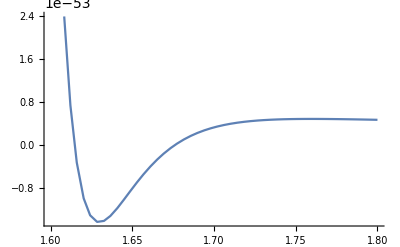

```mathematica
w0=10^(-26);A=2;B=-10^(-30);a=4Pi^2;b=0;
tmin=1.6;tmax=1.8;xval=0.95;
```

```mathematica
w0=10^(-26);A=2;B=-10^(-30);a=4Pi^2;b=4Pi^2;
tmin=1.6;tmax=1.8;xval=0.95;
```

-Graphics-

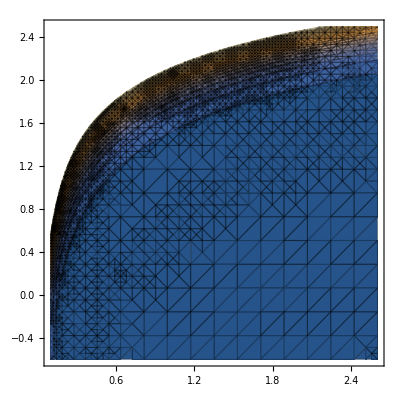

-Graphics3D-

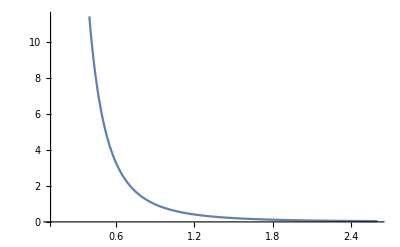

```mathematica
w0=0.6;A=2;B=-0.5;a=4Pi^2+30;b=4Pi^2;
tmin=0.1;tmax=2.6;xval=0.95;
```

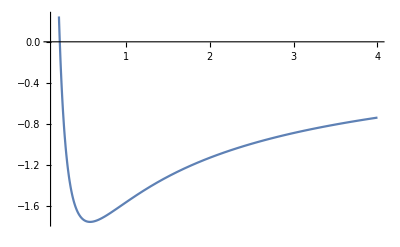

```mathematica
Plot[-Log[5x]/(x)+1/(20x),{x,0.1,4}]
```